```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,100,200,300,400,450,500,530};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

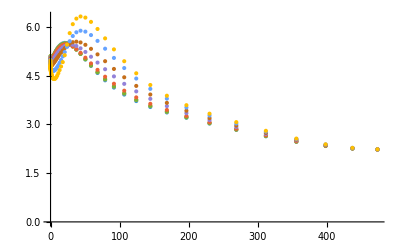

```mathematica
ListPlot[fitdata,PlotRange->All]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
T0p01=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-4.79)/4.79]==0.01,{x,0.01,0.0001,20}],2][[1]][[2]],{i,1,Length[mub]}]
Export["delta0p01.dat",T0p01];
T0p02=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-4.79)/4.79]==0.02,{x,0.01,0.0001,20}],2][[1]][[2]],{i,1,Length[mub]}]
Export["delta0p02.dat",T0p02];
T0p03=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-4.79)/4.79]==0.03,{x,0.01,0.0001,20}],2][[1]][[2]],{i,1,Length[mub]}]
Export["delta0p03.dat",T0p03];
```

{0.325609,0.343457,0.343457,0.390905,0.681095,2.40131,0.27696,0.055765}

{0.8393,0.884844,0.884844,1.0012,1.66951,4.3719,1.10936,0.201752}

FindRoot::jsing: 在点 {x} = {3.94178} 碰到奇异雅克比. 尝试扰动初始点.

{1.46936,1.54755,1.54755,1.74346,2.80127,6.11825,3.94178,0.427216}

```mathematica
4.79*1.03
```

4.9337

```mathematica
4.79*0.97
```

4.6463

```mathematica
Export["mub2.dat",mub]
```

mub2.dat

```mathematica
mub2={0,100,200,300,400,500,550,575,600}
```

{0,100,200,300,400,500,550,575,600}

```mathematica
f=Interpolation[Transpose[{mub,T}],InterpolationOrder->1]
```

Transpose::nmtx: {{0,100,200,300,400,450,500,530},T} 的前两层无法转置.

Interpolation::innd: { 中的第一个参数不包含数据和坐标列表.

Interpolation[Transpose[{{0,100,200,300,400,450,500,530},T}],InterpolationOrder→1]

```mathematica
ListPlot[Table[{x,f[x]},{x,0,600,50}],ScalingFunctions->{Automatic"Log"},PlotRange->All]
```

Transpose::nmtx: {{0,100.,200.,300.,400.,450.,500.,530.},T} 的前两层无法转置.

Interpolation::innd: { 中的第一个参数不包含数据和坐标列表.

Transpose::nmtx: {{0.,100.,200.,300.,400.,450.,500.,530.},T} 的前两层无法转置.

Interpolation::innd: { 中的第一个参数不包含数据和坐标列表.

Transpose::nmtx: {{0.,100.,200.,300.,400.,450.,500.,530.},T} 的前两层无法转置.

General::stop: 在本次计算中，Transpose::nmtx 的进一步输出将被抑制.

Interpolation::innd: { 中的第一个参数不包含数据和坐标列表.

General::stop: 在本次计算中，Interpolation::innd 的进一步输出将被抑制.

ListPlot::sclfn: 缩放函数 {Log Automatic} 不能用来缩放坐标.

-Graphics-

```mathematica
Table[f[mub2[[i]]],{i,1,Length[mub2]}]
Export["delta0p01.dat",%];
```

{Interpolation[Transpose[{{0,100,200,300,400,450,500,530},T}],InterpolationOrder→1][0],Interpolation[Transpose[{{0,100,200,300,400,450,500,530},T}],InterpolationOrder→1][100],Interpolation[Transpose[{{0,100,200,300,400,450,500,530},T}],InterpolationOrder→1][200],Interpolation[Transpose[{{0,100,200,300,400,450,500,530},T}],InterpolationOrder→1][300],Interpolation[Transpose[{{0,100,200,300,400,450,500,530},T}],InterpolationOrder→1][400],Interpolation[Transpose[{{0,100,200,300,400,450,500,530},T}],InterpolationOrder→1][500],Interpolation[Transpose[{{0,100,200,300,400,450,500,530},T}],InterpolationOrder→1][550],Interpolation[Transpose[{{0,100,200,300,400,450,500,530},T}],InterpolationOrder→1][575],Interpolation[Transpose[{{0,100,200,300,400,450,500,530},T}],InterpolationOrder→1][600]}

```mathematica
ListPlot[Transpose[{mub2,f[mub2]}]]
```

Transpose::nmtx: {{0,100,200,300,400,500,550,575,600},Interpolation[{,InterpolationOrder→1][{0,100,200,300,400,500,550,575,600}]} 的前两层无法转置.

Transpose::nmtx: {{0,100.,200.,300.,400.,500.,550.,575.,600.},Interpolation[{,InterpolationOrder→1.][{0,100.,200.,300.,400.,500.,550.,575.,600.}]} 的前两层无法转置.

Transpose::nmtx: {{0.,100.,200.,300.,400.,450.,500.,530.},T} 的前两层无法转置.

General::stop: 在本次计算中，Transpose::nmtx 的进一步输出将被抑制.

Interpolation::innd: { 中的第一个参数不包含数据和坐标列表.

ListPlot::lpn: { 不是由数字或者数对组成的列表.

ListPlot[Transpose[{{0,100,200,300,400,500,550,575,600},Interpolation[Transpose[{{0,100,200,300,400,450,500,530},T}],InterpolationOrder→1][{0,100,200,300,400,500,550,575,600}]}]]

```mathematica
fitdata[[1]][[-1]]
```

{473.079,2.22358}